```mathematica
____________A и B (Δ)___________
```

```mathematica
sol =Flatten[NSolve[{-h/a +c11 a^2 / 2 + c12 b^2/ 2 +δ 2π-Δ 2π== 0  /. {h->.00005,δ->.001, c22->100, c12->80, c11->-90},-h/b+c12 a^2 / 2 + c22 b^2 / 2 -δ 2π-Δ 2π== 0/. {h->.00005,δ->.001, c22->100, c12->80, c11->-90}} ,{a,b}]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
sol1 =Flatten[NSolve[{c11 A / 2 + c12 B/ 2 +δ 2π-Δ 2π== 0  /. {h->0,δ->.001, c22->100, c12->80, c11->-90},c12 A/ 2 + c22 B/ 2 -δ 2π-Δ 2π== 0/. {h->0,δ->.001, c22->100, c12->80, c11->-90}} ,{A,B}]];
```

```mathematica
Flatten[Solve[{c11 A / 2 + c12 B/ 2 +δ 2π-Δ 2π== 0 ,c12 A/ 2 + c22 B/ 2 -δ 2π-Δ 2π== 0} ,{A,B}]]
```

{A→(4 (c12 π δ+c22 π δ+c12 π Δ-c22 π Δ))/(c12^2-c11 c22),B→-(4 (c11 π δ+c12 π δ+c11 π Δ-c12 π Δ))/(c12^2-c11 c22)}

```mathematica
Solve[c12 π δ+c22 π δ+c12 π Δ-c22 π Δ==0,Δ]
Solve[c11 π δ+c12 π δ+c11 π Δ-c12 π Δ==0,Δ]
```

{{Δ→(-c12 δ-c22 δ)/(c12-c22)}}

{{Δ→(-c11 δ-c12 δ)/(c11-c12)}}

```mathematica
la={a/.{sol[[1]]},a/. sol[[3]],a/. sol[[5]],a/.{sol[[7]]},a/. sol[[9]],a/. sol[[11]],a/.{sol[[13]]},a/. sol[[15]],a/. sol[[17]]};
```

```mathematica
la0 = {A/.{sol1[[1]]}};
```

```mathematica
lb={b/.{sol[[2]]},b/. sol[[4]],b/. sol[[6]],b/.{sol[[8]]},b/. sol[[10]],b/. sol[[12]],b/.{sol[[14]]},b/. sol[[16]],b/. sol[[18]]};
```

```mathematica
lb0 = {B/.{sol1[[2]]}};
```

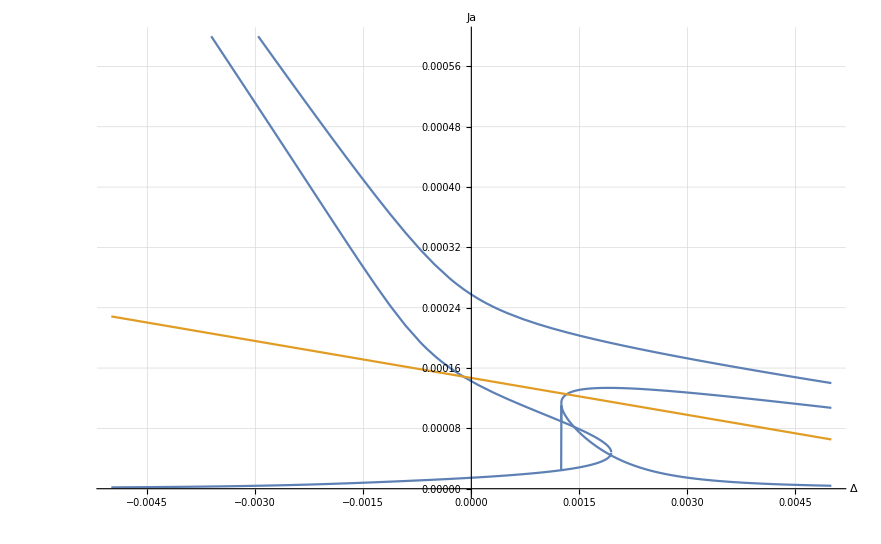

```mathematica
Plot[{ la^2, la0}, {Δ, -.005, .005},PlotRange->{0,0.0006},LabelStyle->Directive[Black, 25],GridLines->Automatic,AxesLabel->{"Δ","Ja"}]
```

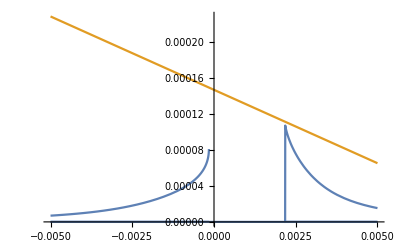

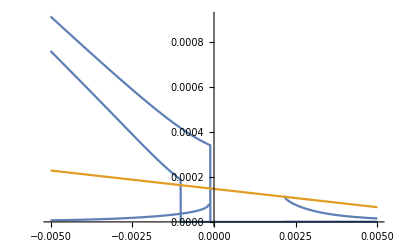

```mathematica
Plot[{((Sign[Sign[detpπ]+Sign[detp0]+1]+1)/2)((Sign[dopp2]+1)/2)la^2, la0}, {Δ, -.005, .005}]
Plot[{((Sign[Sign[detpπ]+Sign[detp0]+1]+1)/2)((Sign[dopp1]+1)/2)la^2, la0}, {Δ, -.005, .005}]
```

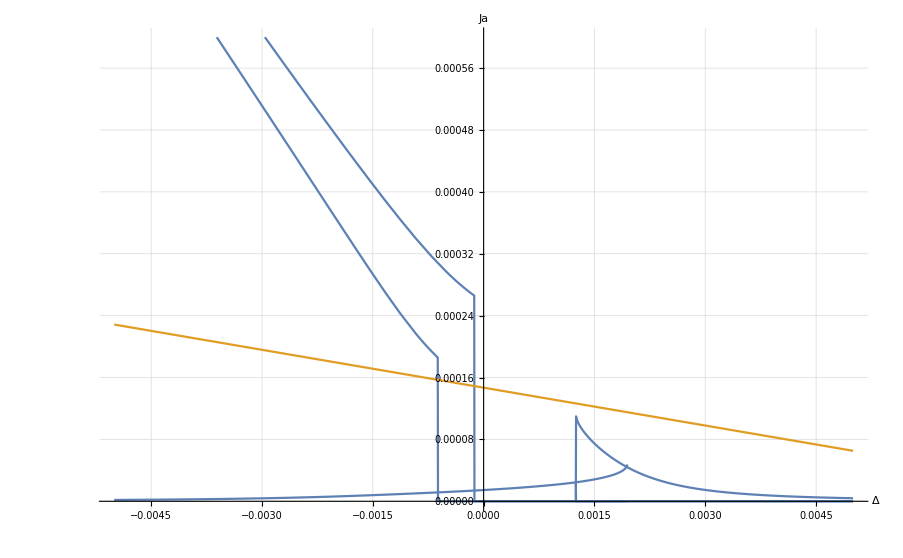

```mathematica
xPlot=Plot[{((Sign[Sign[detpπ]+Sign[detp0]+1]+1)/2)((Sign[Sign[dopp1]+Sign[dopp2]+1]+1)/2)la^2, la0}, {Δ, -.005, .005},PlotRange->{0,0.0006},LabelStyle->Directive[Black, 25],GridLines->Automatic,AxesLabel->{"Δ","Ja"}]
```

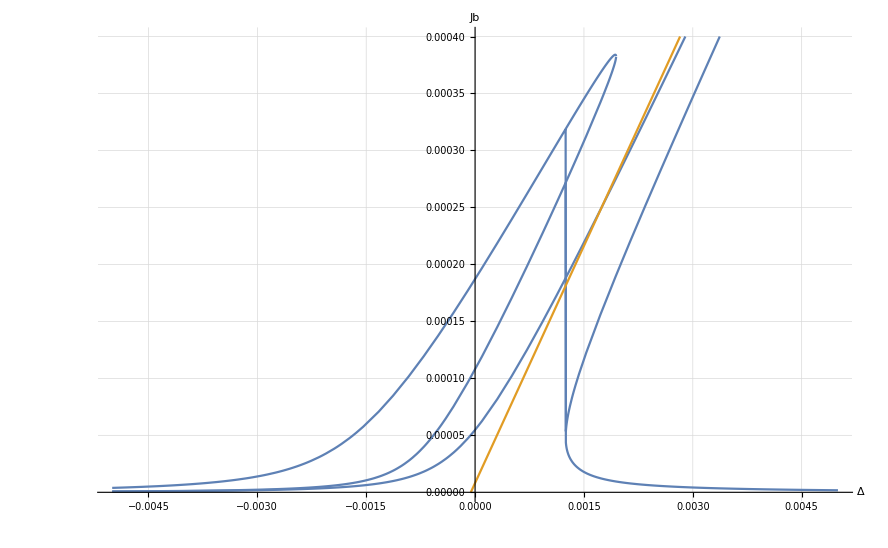

```mathematica
Plot[{ lb^2, lb0}, {Δ, -.005, .005},PlotRange->{0,0.0004},LabelStyle->Directive[Black, 25],GridLines->Automatic,AxesLabel->{"Δ","Jb"}]
```

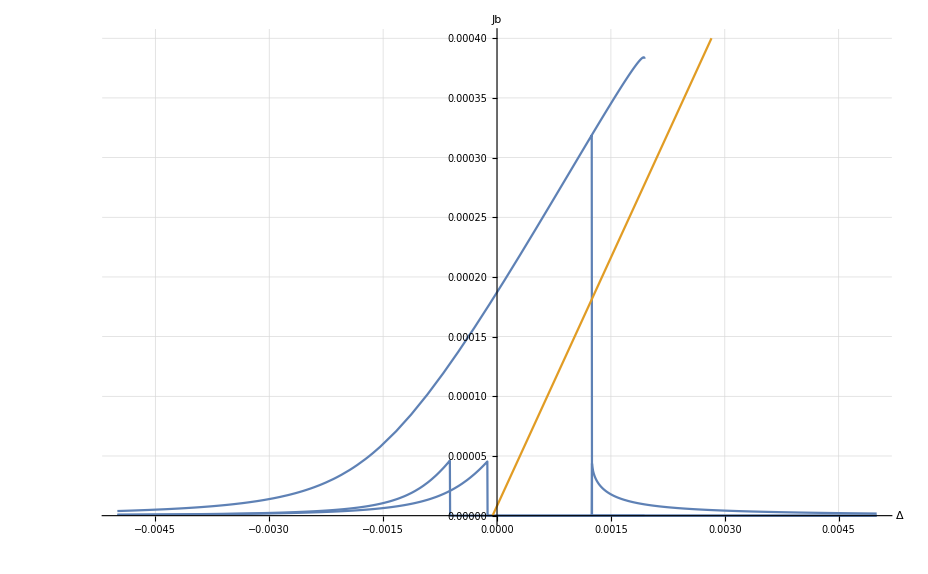

```mathematica
yPlot=Plot[{((Sign[Sign[detpπ]+Sign[detp0]+1]+1)/2)((Sign[Sign[dopp1]+Sign[dopp2]+1]+1)/2)lb^2, lb0}, {Δ, -.005, .005},PlotRange->{0,0.0004},LabelStyle->Directive[Black, 25],GridLines->Automatic,AxesLabel->{"Δ","Jb"}]
```

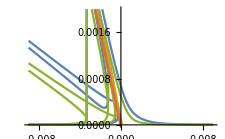

```mathematica
Plot[{la^2, la0, lb^2 , lb0}, {Δ, -.009, .009},PlotRange->{0,0.002}]
```

```mathematica
___________вторые производные (проверка на устойчивость)____ странно, получилось что всегда устойчиво..___
```

```mathematica
H=2h Sqrt[Ja]Cos[ϕa]+2h Sqrt[Jb]Cos[ϕb]+c11 Ja^2/4+c12 Ja Jb/2+c22 Jb^2/4+2π δ(Ja-Jb)-2π Δ(Ja+Jb);
```

```mathematica
M=({{D[H,{ϕa,2}], D[H,ϕa,Ja], D[H,ϕa,ϕb], D[H,ϕa,Jb]}, {D[H,ϕa,Ja], D[H,{Ja,2}], D[H,Ja,ϕb], D[H,Ja,Jb]}, {D[H,ϕa,ϕb], D[H,Ja,ϕb], D[H,{ϕb,2}], D[H,ϕb,Jb]}, {D[H,ϕa,Jb], D[H,Ja,Jb], D[H,ϕb,Jb], D[H,{Jb,2}]}})/.{ϕa->0,ϕb->0};
MatrixForm[M]
```

(-2 h √Ja | 0 | 0 | 0
0 | c11/2-h/(2 Ja^(3/2)) | 0 | c12/2
0 | 0 | -2 h √Jb | 0
0 | c12/2 | 0 | c22/2-h/(2 Jb^(3/2)))

```mathematica
m1=-√Ja h
m2=-√Ja(c11/2-h/(2 Ja^(3/2)))
m3=-√Ja(c11/2-h/(2 Ja^(3/2)))(-√Jb)h h
m4=Simplify[Simplify[Det[M]]/(4 h h Sqrt[Ja Jb])]
```

-h √Ja

-(c11/2-h/(2 Ja^(3/2))) √Ja

h^2 (c11/2-h/(2 Ja^(3/2))) √Ja √Jb

(h^2+(-c12^2+c11 c22) Ja^(3/2) Jb^(3/2)-h (c11 Ja^(3/2)+c22 Jb^(3/2)))/(4 (Ja Jb)^(3/2))

```mathematica
Simplify[-hAB hAB+hAA hBB]
```

1/4 (-c12^2+(c11-h/A^(3/2)) (c22-h/B^(3/2)))

```mathematica
ϕa->0,ϕb->0: отрицательно определено когда c11/2-h/(2 Ja^(3/2))<0,detM>0
ϕa->0,ϕb->π и наоборот: знакопеременно
```

```mathematica
ϕa->π,ϕb->π: положительно определено когда c11/2+h/(2 Ja^(3/2))>0,detM>0
```

```mathematica
hA=-h/Sqrt[A] + δ - Δ +c11 A / 2 + c12 B/ 2;
```

```mathematica
hB = -h/Sqrt[B] - δ - Δ +c12 A / 2 + c22 B/ 2;
```

```mathematica
hAA=D[hA,A]
```

c11/2+h/(2 A^(3/2))

```mathematica
hBB=D[hB,B]
```

c22/2+h/(2 B^(3/2))

```mathematica
hAB = D[hA,B]
```

c12/2

```mathematica
detπ=(-c12/2 c12/2+(c11/2+h/(2 A^(3/2))) (c22/2+h/(2 B^(3/2))))/.{A->a^2,B->b^2};
det0=(-c12/2 c12/2+(c11/2-h/(2 A^(3/2))) (c22/2-h/(2 B^(3/2))))/.{A->a^2,B->b^2};
dop1=(-c11/2+h/(2 Ja^(3/2)))/.{Ja->a^2,Jb->b^2};
dop2=(c11/2+h/(2 Ja^(3/2)))/.{Ja->a^2,Jb->b^2};
```

```mathematica
detpπ=Table[(detπ/.{a->(a/.sol[[i]]),b->(b/.sol[[i+1]])})/.{h->.00005,δ->.001, c22->100, c12->80, c11->-90},{i,1,17,2}];
detp0=Table[(det0/.{a->(a/.sol[[i]]),b->(b/.sol[[i+1]])})/.{h->.00005,δ->.001, c22->100, c12->80, c11->-90},{i,1,17,2}];
dopp1=Table[(dop1/.{a->(a/.sol[[i]]),b->(b/.sol[[i+1]])})/.{h->.00005,δ->.001, c22->100, c12->80, c11->-90},{i,1,17,2}];
dopp2=Table[(dop2/.{a->(a/.sol[[i]]),b->(b/.sol[[i+1]])})/.{h->.00005,δ->.001, c22->100, c12->80, c11->-90},{i,1,17,2}];
```

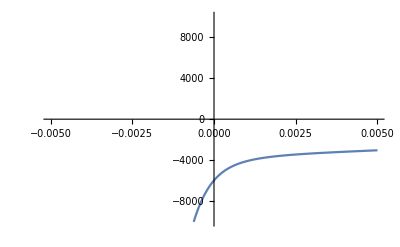
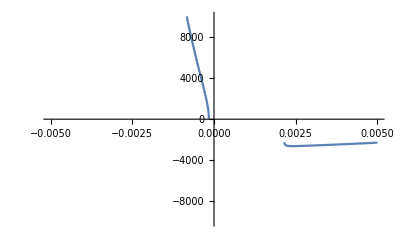
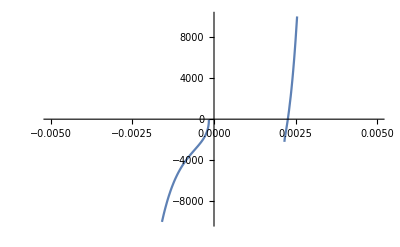

```mathematica
Table[Plot[detp[[i]],{Δ,-.005,.005},PlotRange->{-10000,10000}],{i,1,3}]
```

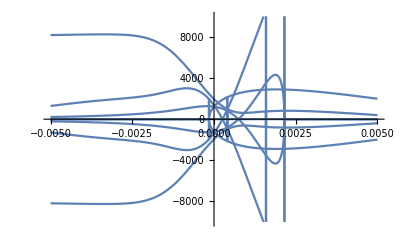

```mathematica
Plot[Im[detp],{Δ,-.005,.005},PlotRange->{-10000,10000}]
```

```mathematica
___________Δ(B) (при разных A) __и__ Δ(A) (при разных B)________
```

```mathematica
solDeltA=Flatten[Solve[{h Sqrt[B]/Sqrt[A] + δ + Δ +c11 A / 2 + c12 B/ 2 == 0  /. {h->.1,δ->.1, c22->.1 coef, c12->.2 coef, c11->.1 coef},Sqrt[A] h/Sqrt[B] - δ + Δ+c12 A / 2 + c22 B / 2 == 0/. {h->.1,δ->.1, c22->.1 coef, c12->.2 coef, c11->.1 coef}} ,{Δ,A}]];
```

```mathematica
lDelt={Δ/.solDeltA[[1]],Δ/. solDeltA[[3]]};
```

```mathematica
solDeltA0=Flatten[Solve[{ δ + Δ +c11 A / 2 + c12 B/ 2 == 0  /.{h->.1,δ->.1, c22->.1 coef, c12->.2 coef, c11->.1 coef},- δ + Δ+c12 A / 2 + c22 B / 2 == 0/.{h->.1,δ->.1, c22->.1 coef, c12->.2 coef, c11->.1 coef}} ,{Δ,A}]];
```

```mathematica
lDelt0={Δ/.solDeltA0[[1]]};
```

```mathematica
Manipulate[Plot[{lDelt/.{coef->asf},lDelt0 /.{coef->asf}}, {B, -5, 10},WorkingPrecision->10],{asf,0.001,1}]
```

```mathematica
solDeltB=Flatten[Solve[{h/Sqrt[A] + δ + Δ +c11 A / 2 + c12 B/ 2 == 0  /. {h->.1,δ->.1, c22->.1 coef, c12->.2 coef, c11->.1 coef},h/Sqrt[B] - δ + Δ+c12 A / 2 + c22 B / 2 == 0/. {h->.1,δ->.1, c22->.1 coef, c12->.2 coef, c11->.1 coef}} ,{Δ,B}]];
```

```mathematica
lDeltB={If[Re[haa/.{solDeltB[[2]]}]<0 ,1,0]If[Im[A/.{solDeltB[[2]]}]==0 ,1,0]Δ/.solDeltB[[1]],If[Re[haa/.{solDeltB[[4]]}]<0 ,1,0]If[Im[A/.{solDeltB[[4]]}]==0 ,1,0]Δ/. solDeltB[[3]],If[Re[haa/.{solDeltB[[6]]}]<0 ,1,0]If[Im[A/.{solDeltB[[6]]}]==0 ,1,0]Δ/. solDeltB[[5]]};
```

```mathematica
solDeltB0=Flatten[Solve[{ δ + Δ +c11 A / 2 + c12 B/ 2 == 0  /. {h->.1,δ->.1, c22->.1 coef, c12->.2 coef, c11->.1 coef},- δ + Δ+c12 A / 2 + c22 B / 2 == 0/. {h->.1,δ->.1, c22->.1 coef, c12->.2 coef, c11->.1 coef}} ,{Δ,B}]];
```

```mathematica
lDeltB0={Δ/.solDeltB0[[1]]};
```

```mathematica
Manipulate[Plot[{lDeltB/.{coef->asf},lDeltB0 /.{coef->asf}}, {A, -5, 10},WorkingPrecision->10],{asf,0,1}]
```

```mathematica
lhbb={hbb/.{solDeltB[[2]]},hbb/.{solDeltB[[4]]},hbb/.{solDeltB[[6]]}};
```

```mathematica
//оказалось,что 3я пара - неустойчива, а вторая (которая начинается с 0) устойчива только до некоторого А
```

```mathematica
Manipulate[Plot[lhbb/.{coef->asf},{A, 0, 10},WorkingPrecision->10],{asf,.1,1}]
```

```mathematica
lhaa={haa/.{solDeltA[[2]]},haa/.{solDeltA[[4]]},haa/.{solDeltA[[6]]}};
```

```mathematica
Manipulate[Plot[lhaa/.{coef->asf},{B, 0, 10},WorkingPrecision->10],{asf,.1,1}]
```

```mathematica
______________B(A)___(при разных Δ)_______
```

```mathematica
lB={B/.solDeltB[[2]],B/. solDeltB[[4]],B/.solDeltB[[6]]};
```

```mathematica
lB0={B/.solDeltB0[[2]]};
```

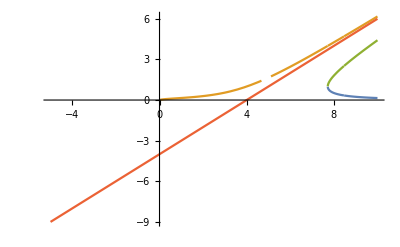

```mathematica
Plot[{lB,lB0}, {A, -5, 10}]
```

```mathematica
_________________________________==========++++++++++++++++++++++++++++++++++++++=========+________
```

```mathematica
sol =Flatten[NSolve[{-h1 a^2Sin[ϕa]+a b Sin[2 ϕa](h111 Cos[ϕb]+h112 Sin[ϕb])+b^2Sin[ϕa](h121 Cos[ϕb]+h122 Sin[ϕb]) == 0 ,-h1 a Cos[ϕa]+ b Cos[2 ϕa](h111 Cos[ϕb]+h112 Sin[ϕb])+b^2Cos[ϕa](h121 Cos[ϕb]+h122 Sin[ϕb])/a+n+1/3+Δ-δ==0,-h2 b^2Sin[ϕb]+a b Sin[2 ϕb](h211 Cos[ϕa]+h212 Sin[ϕa])+a^2Sin[ϕb](h221 Cos[ϕa]+h222 Sin[ϕa])==0,-h2 b Cos[ϕb]+a  Cos[2 ϕb](h211 Cos[ϕa]+h212 Sin[ϕa])+a^2Cos[ϕb](h221 Cos[ϕa]+h222 Sin[ϕa])/b+n+1/3+Δ+δ==0}/.{h1->1,h2->1,h111->0,h112->0,h121->0,h122->0,h211->0,h212->0,h221->0,h222->0} ,{a,b,ϕa,ϕb}]];
```

```mathematica
%6[[16]]
```

ϕb→ConditionalExpression[6.28319 C[2],C[2]∈ℤ]

```mathematica
ϕb/.{sol[[4]],Δ->0.5}
ϕb/.{sol[[8]],Δ->0.5}
ϕb/.{sol[[12]],Δ->0.5}
ϕb/.{sol[[16]],Δ->0.5}
```

ConditionalExpression[1. (3.14159+6.28319 C[2]),C[2]∈ℤ]

ConditionalExpression[6.28319 C[2],C[2]∈ℤ]

ConditionalExpression[1. (3.14159+6.28319 C[2]),C[2]∈ℤ]

ConditionalExpression[6.28319 C[2],C[2]∈ℤ]

```mathematica
sol1 =Flatten[NSolve[{-h1 a^2Sin[ϕa]+a b Sin[2 ϕa](h111 Cos[ϕb]+h112 Sin[ϕb])+b^2Sin[ϕa](h121 Cos[ϕb]+h122 Sin[ϕb]) == 0 ,-h1 a Cos[ϕa]+ b Cos[2 ϕa](h111 Cos[ϕb]+h112 Sin[ϕb])+b^2Cos[ϕa](h121 Cos[ϕb]+h122 Sin[ϕb])/a+n+1/3+Δ-δ==0,-h2 b^2Sin[ϕb]+a b Sin[2 ϕb](h211 Cos[ϕa]+h212 Sin[ϕa])+a^2Sin[ϕb](h221 Cos[ϕa]+h222 Sin[ϕa])==0,-h2 b Cos[ϕb]+a  Cos[2 ϕb](h211 Cos[ϕa]+h212 Sin[ϕa])+a^2Cos[ϕb](h221 Cos[ϕa]+h222 Sin[ϕa])/b+n+1/3+Δ+δ==0}/.{h1->1,h2->1,h111->0,h112->0,h121->0,h122->0,h211->0,h212->0,h221->0,h222->0,ϕa->0,ϕb->0} ,{a,b}]]
```

{a→-1. (-0.333333-1. n+1. δ-1. Δ),b→-1. (-0.333333-1. n-1. δ-1. Δ)}

```mathematica
(a/.{sol[[1]]})/.{Δ->a1,n->2}
```

0.333333 (-7.-3. a1+3. δ)

```mathematica
Manipulate[Plot[{(a/.{sol[[1]]})/.{Δ->a1,n->0},(a/.{sol[[5]]})/.{Δ->a1,n->0},(a/.{sol[[9]]})/.{Δ->a1,n->0},(a/.{sol[[13]]})/.{Δ->a1,n->0}},{δ,0,0.5}],{a1,-5,5}]
```

```mathematica
Manipulate[Plot[{(b/.{sol[[2]]})/.{Δ->a1,n->0},(b/.{sol[[6]]})/.{Δ->a1,n->0},(b/.{sol[[10]]})/.{Δ->a1,n->0},(b/.{sol[[14]]})/.{Δ->a1,n->0}},{δ,0,0.5}],{a1,-5,5}]
```